```mathematica
grad = {212,212,213,215,213,213,213}
```

{212,212,213,215,213,213,213}

```mathematica
minute = {42,42,5,22,58,53,44}
```

{42,42,5,22,58,53,44}

```mathematica
second = {37,19,28,52,30,30,55}
```

{37,19,28,52,30,30,55}

```mathematica
minute = minute/60
```

{7/10,7/10,1/12,11/30,29/30,53/60,11/15}

```mathematica
second = second/3600
```

{37/3600,19/3600,7/900,13/900,1/120,1/120,11/720}

```mathematica
data = grad+minute+second
```

{765757/3600,765739/3600,95891/450,193843/900,8559/40,25667/120,153899/720}

```mathematica
data = data - (160+11/60+57/3600)
```

{2363/45,94511/1800,190411/3600,39731/720,64531/1200,21477/400,96389/1800}

```mathematica
data = data - 0.0
```

{52.5111,52.5061,52.8919,55.1819,53.7758,53.6925,53.5494}

```mathematica
plotdata = {{data⟦1⟧,579},{data⟦2⟧, 586},{data⟦3⟧,546.07},{data⟦4⟧, 435},{data⟦5⟧, 491.61},{data⟦6⟧, 497.36},{data⟦7⟧,503}}
```

{{52.5111,579},{52.5061,586},{52.8919,546.07},{55.1819,435},{53.7758,491.61},{53.6925,497.36},{53.5494,503}}

```mathematica
line = LinearModelFit[plotdata,{1,Log@x},x]
```

FittedModel[12576.9-3030.57 Log[x]]

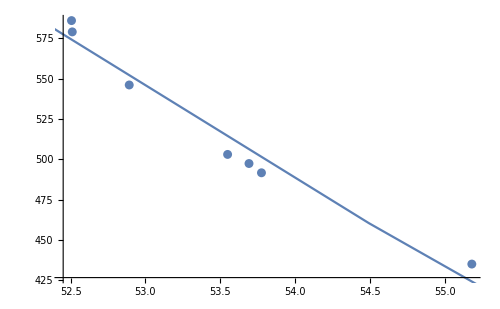

```mathematica
Show[
ListPlot[plotdata,ImageSize->500],
Plot[Normal@line,{x,0,600}]
]
```

```mathematica
Sin[(160+48/60+55/3600-43+ 46/60+32/3600+62+57/60+37/3600)/2+0.0]/Sin[62+57/60+37/3600+0.0]
```

2.53483